```mathematica
nStat = 1.37*10^8*1000;
alpha = 2.3 * 10^-19;
beta = 2.3 * 10 ^ -18;
aThresh = 70 * 10^-9;
exp = 2.5;
gamma = 0.005545;
```

```mathematica
aSol=NDSolve[
{a'[t]==-gamma*a[t]+(alpha+beta/((aThresh/a[t])^exp+1))*nStat,a[0]==10^-20},a,{t,0,1000}
];
```

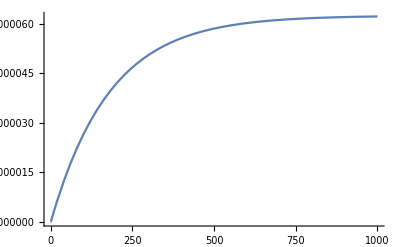

```mathematica
Plot[Evaluate[a[t]/.aSol],{t,0,1000},PlotRange->All]
```